# Chapter. Chronopotentiometry

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
Off[FindRoot::"cvnwt"];
Off[FindRoot::"cvmit"];
Off[FindRoot::"bddir"];
Off[FindRoot::"lstol"];
Off[FindRoot::"nlnum"];
Off[General::"ovfl"];
Off[General::"unfl"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->163,

PageHeaders-> {{Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12], Cell[TextData[{"Chronopotentiometry"}],FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Current reversal","Successive electron transfers","Finite Difference Simulation","Summary","Further Reading"},#]&)]],FontFamily->"Arial",FontSize->12], Cell[TextData[{CounterBox["Page"]}],FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];(*allows the creation of new symbols*)
```

```mathematica
ClearNotations[];
Symbolize[Subscript[𝔼, _]];
Symbolize[Subscript[t, _]];
Symbolize[c^_];
Symbolize[Subscript[n, _]];
Symbolize[Subscript[c, _]];
```

```mathematica
SetOptions[Plot,
Axes-> False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
Frame->True,
GridLines->None,
ImageSize->288];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
FrameLabel->None,
Frame->True,
FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,x,{0.015,0}},{x,Floor[min],Ceiling[max],steps}],Table[{x,"",{0.0075,0}},{x,Floor[min],Ceiling[max],steps/divs}]]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,Floor[min],Ceiling[max],steps}],Table[{x,"",{0.0075,0}},{x,Floor[min],Ceiling[max],steps/divs}]]];
```

```mathematica
optionB={
FrameTicks->{ticks1[-.2,1.2,.2,5],ticks1[-20,15,10,5],ticks2[-.2,1.2,.2,5],ticks2[-20,15,10,5]},
FrameLabel->{
Style["t",FontFamily-> "Times New Roman",Black,Italic,0],
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic,Black,10],
None,None}
};
```

```mathematica
optionC={
FrameTicks->{ticks1[-15,15,5,5],ticks1[-.1,.5,.1,5],ticks2[-15,15,5,5],ticks2[-.1,.5,.1,5]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Black,Italic,10],
Style["dt/dE",FontFamily-> "Times New Roman",Italic,Black,10],
None,None},
RotateLabel-> False};
```

```mathematica
optionD={
FrameTicks->{ticks1[0,500,100,5],ticks1[-15,10,5,5],ticks2[0,500,100,5],ticks2[-15,10,5,5]},
FrameLabel->{
Style["t",FontFamily-> "Times New Roman",Black,Italic,10],
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic,Black,10],None,None}};
```

```mathematica
optionE={
FrameTicks->{ticks1[0,1600,400,4],ticks1[-30,10,5,5],ticks2[0,1600,400,4],ticks2[-30,10,5,5]},
FrameLabel->{
Style["t",FontFamily-> "Times New Roman",Black,Italic,10],
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic,Black,10],None,None}
};
```

Mathematica Version 4.0 and above

Users of versions of Mathematica below 4.0 first need to load the package LaplaceTransform.m which is located in the Calculus subdirectory of the StandardPackages subdirectory in the directory AddOns. To get version 4 to run identically to version 3 execute this work around at the beginning of all notebooks which use Laplace transform. This was written for me by Lou Dandria at Wolfram when I was there in 2000.

```mathematica
If[$VersionNumber>3.,
Unprotect[LaplaceTransform];

LaplaceTransform[Derivative[d__][c][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][C[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][u][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][U[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][v][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][V[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[c[args__],t_,s_]:=With[{pos=Position[{args},t]},C[s][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1]

(*Protect[LaplaceTransform];*)];
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

In chronopotentiometric experiments the current is fixed and the change in potential versus time is measured. The analytical solution for controlled current chronopotentiometry is obtained by using Laplace transforms following similar procedures to those described in earlier chapters. We begin with Fick’s second law

(∂c_O(x,t))/(∂t)=(∂^2 c_O(x,t))/(∂x^2)

(∂c_R(x,t))/(∂t)=(∂^2 c_R(x,t))/(∂x^2)

The initial conditions, assuming that R is not initially present, are

c_O(x,0)=c_O^*
c_R(x,0)=0

and the boundary conditions

c_O(∞,t)=c_O^*
c_R(∞,t)=0

(D_O((∂c_O(x,t))/(∂x)))_(x=0)+(D_R((∂c_R(x,t))/(∂x)))_(x=0)=0

i/(n F A)=(D_O((∂c_O(x,t))/(∂x)))_(x=0)

Applying Laplace transforms using the steps outlined in §5.2 we arrive at

```mathematica
ClearAll[soln];
soln[x_]:=c^✶/s+ⅇ^(-(√s x)/(√𝒟)) C[1];
```

(c^-)_O(x,s)=c_O^*/s+B exp(-(x(s/D_O))^(1/2))

where B is a constant. To evaluate the constant B we refer to the transformed boundary condition:

```mathematica
ClearAll[𝒟,c,x,t,i,nFA];

laplaceDemo=LaplaceTransform[i/nFA==𝒟*D[c[x,t],x],t,s]
```

i/(nFA s)==𝒟 C[s]'[x]

Taking the derivative of eqn (Chapter.EquationNumbered) at x=0 gives

```mathematica
soln'[0]
```

-(√s C[1])/(√𝒟)

Therefore

```mathematica
solveC=Solve[i/(nFA s)==𝒟*soln'[0],C[1]]
```

{{C[1]→-i/(nFA s^(3/2) √𝒟)}}

Substituting this into eqn (Chapter.EquationNumbered) gives

```mathematica
soln2=Simplify[soln[x]/.solveC,{𝒟>0,x>0}]
```

{c^✶/s-(ⅇ^(-x √(s/𝒟)) i)/(nFA s^(3/2) √𝒟)}

Therefore (c^-)_O(x,s) is given by

(c^-)_O(x,s)=c_O^*/s-i/(n F A s^(3/2)D_O)exp(-(x(s/D_O))^(1/2))

The inverse transform of this equation is (unfortunately, due to a bug in the versions of Mathematica below V4.2 the inverse transform is not found).

```mathematica
soln3= Simplify[InverseLaplaceTransform[soln2⟦1⟧, s, t],{x>0,t>0,𝒟>0}]
```

c^✶-(i ((2 ⅇ^(-x^2/(4 t 𝒟)) √(t 𝒟))/(√π)-x Erfc[x/(2 √(t 𝒟))]))/(nFA 𝒟)

Replacing the error function with the error function complement, erfc,we have:

```mathematica
soln3=soln3/.Erf[x_]:> (1-Erfc[x])//Simplify
```

c^✶-(i ((2 ⅇ^(-x^2/(4 t 𝒟)) √(t 𝒟))/(√π)-x Erfc[x/(2 √(t 𝒟))]))/(nFA 𝒟)

c_O(x,t)=c_O^*-i/(n F A D_O)(((4tD)/π)^(1/2)exp(-x^2/(4t D_O))-x erfc(x/(4t D_O)^(1/2)))

At x=0 we the solution reduces to:

```mathematica
soln3/.x-> 0
```

c^✶-(2 i √(t 𝒟))/(nFA √π 𝒟)

The concentration at the electrode surface is therefore given by

c_O(0,t)=c_O^*-(2i)/(n F A)(t/(π D_O))^(1/2)

Solving for the concentration of R at the electrode surface gives

c_R(0,t)=(2i)/(n F A)(t/(π D_R))^(1/2)

After a period of time, τ, referred to as the transition time, the term of the far right of eqn (Chapter.EquationNumbered) will equal the bulk concentration and the concentration of O at the electrode surface will be zero. Therefore

iτ^(1/2)/c_O^*=(n F (A(π D_O))^(1/2))/2

Equation (Chapter.EquationNumbered) is known as the Sand equation. Note that the transition time is independent of the kinetics of the reaction. For a reversible reaction the potential versus time plot can be found by substituting eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) into the Nernst equation.

E=E°'+RT/(2n F)ln D_R/D_O+RT/(n F)ln(τ^(1/2)-t^(1/2))/t^(1/2)

Experimentally potential is measured versus time. The resultant chronopotentiogram has a sigmoidal shape.

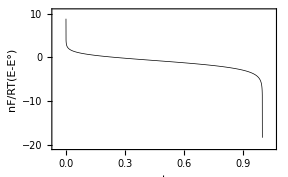

```mathematica
τ=1.;
chronoPlot=Plot[Log[(-√t+√τ)/(√t)],{t,0,1},Evaluate[optionB],PlotRange->{{-0.05,1.05},{-20.5,10.5}},RotateLabel-> True]
```

Fig. Chapter.FigureCaption  A typical chronopotentiogram.

When t = τ/4, E equals the quarter wave potential

E_(1/4)=E°'+RT/(2n F)ln D_R/D_O

The chronopotentiogram can be transformed to look similar to a voltammogram by plotting d t/d E versus E. After solving for t,

```mathematica
ClearAll[ℰ,τ];
(*ℰ=nF/RT*(𝔼- Subscript[𝔼, 1/4])*)
soln4=Quiet@Solve[ℰ==Log[ (τ^(1/2)-t^(1/2))/t^(1/2)],t]
```

{{t→τ/((-1+ⅇ^ℰ)^2)},{t→τ/((1+ⅇ^ℰ)^2)}}

The derivative of eqn (Chapter.EquationNumbered) is

```mathematica
dtdE=D[soln4⟦All,1,2⟧,ℰ]//Simplify
```

{-(2 ⅇ^ℰ τ)/((-1+ⅇ^ℰ)^3),-(2 ⅇ^ℰ τ)/((1+ⅇ^ℰ)^3)}

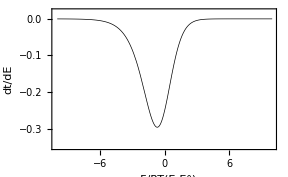

```mathematica
τ=1.;
Plot[dtdE⟦2⟧,{ℰ,-10,10},Evaluate[optionC],PlotRange->{{-10.1,10},{-.35,0.02}}]
```

Fig. Chapter.FigureCaption  A typical derivative chronopotentiogram.

The maximum of the derivative plot occurs at a dimensionless potential of -ln  2.

## Chapter.Section Current reversal

If the current is reversed after a time t_1 the current is given by

i(t)=i-2i S(t-t_1)

where S(t-t_1) is the unit step function which is zero for t<t_1and one for t≥t_1. The Laplace transform of this is

```mathematica
Simplify[LaplaceTransform[i[t]== i-2*i*UnitStep[t-Subscript[t, 1]],t,s],t>0&&Subscript[t, 1]>0]
```

i[s]==(i-2 ⅇ^(-s t_1) i)/s

The transformed surface boundary condition now becomes

```mathematica
ClearAll[𝒟,c,x,t,i,nFA];

res1=Simplify[LaplaceTransform[(i-2*i*UnitStep[t-Subscript[t, 1]])/nFA==𝒟*D[c[x,t],x],t,s],t>0&&Subscript[t, 1]>0]
```

(i-2 ⅇ^(-s t_1) i)/(nFA s)==𝒟 C[s]'[x]

By taking the derivative of eqn (Chapter.EquationNumbered) we can solve for the integration constant B (C[1]).

```mathematica
solveC=Solve[res1⟦1⟧== 𝒟*soln'[0],C[1]]
```

{{C[1]→-(ⅇ^(-s t_1) (-2+ⅇ^(s t_1)) i)/(nFA s^(3/2) √𝒟)}}

Substituting this into eqn (Chapter.EquationNumbered) with x=0 gives

```mathematica
soln2=soln[0]/.solveC//Simplify
```

{c^✶/s-(ⅇ^(-s t_1) (-2+ⅇ^(s t_1)) i)/(nFA s^(3/2) √𝒟)}

The inverse transform of this equation is

```mathematica
soln3=Apart[InverseLaplaceTransform[soln2⟦1⟧, s, t]]
```

c^✶-(2 i √t)/(nFA √π √𝒟)+(4 i √(t-t_1) HeavisideTheta[t-t_1])/(nFA √π √𝒟)

c_O(0,t)=c_O^*-(2i)/(n F (A(π D_O))^(1/2))(t^(1/2)-2S(t-t_1)(t-t_1)^(1/2))

If the current reversal takes place at the first transition time, i.e. t_1=τ_1, then a second transition time, τ_2, is reached when the surface concentration of R is zero which occurs at time t=τ_1 + τ_2 . Since the surface concentration of R is

c_R(0,t)=(2i)/(n F (A(π D_R))^(1/2))(t^(1/2)-2S(t-t_1)(t-t_1)^(1/2))

the second transition time occurs at

t^(1/2)-2(t-t_1)^(1/2)=0

so that

```mathematica
ClearAll[τ];

Solve[(t^(1/2)-2*(t-Subscript[τ, 1])^(1/2)/.t->(Subscript[τ, 1]+Subscript[τ, 2]))== 0,Subscript[τ, 2]]
```

{{τ_2→τ_1/3}}

## Chapter.Section Successive electron transfers

An interesting effect arises in constant current chronopotentiometry when a second electron transfer reaction occurs at potentials sufficiently removed from the first reaction that the transition time for the first reaction is reached before the second reaction commences. This could be either a two component system or an EE mechanism. Thus for the reactions

O_1+n_1 e ⇌ R_1
O_2+n_2 e ⇌ R_2

at times up to the first transition time the amount of O_2 reduced is undetectable so that the second reaction can be ignored. After the first transition time has been reached the potential becomes more negative and eventually O_2 starts to be reduced but even though the surface concentration of O_1 is zero O_1 continues to diffuse to the electrode surface to be reduced. The current applied to the cell is therefore partitioned between the fluxes of the two components

n_1(D_O_1((∂c_O_1(x,t))/(∂x)))_(x=0)+n_2(D_O_2((∂c_O_2(x,t))/(∂x)))_(x=0)=i/(F A)

From eqn (Chapter.EquationNumbered) the Laplace transformed concentrations at the surface, x=0, will be

c_O_1^*/s-c_O_1(0,s)=i_1/(n_1 F A s^(3/2) D_O_1^(1/2))

c_O_2^*/s-c_O_2(0,s)=i_2/(n_2 F A s^(3/2) D_O_2^(1/2))

where i_1 and i_2 are the fractions of the total current being used to reduce O_1 and O_2 respectively. At time t > τ_1 c_O_1(0,s)=0 and since i_1+i_2=i for equal diffusion coefficients we have

n_2 D^(1/2)c_O_2(0,s)=(n_1 D^(1/2)c_O_1^*+n_2 D^(1/2)c_O_2^*)/s-i/(F A s^(3/2))

At the second transition time c_O_2(0,s)=0 therefore

(n_1 D^(1/2)c_O_1^*+n_2 D^(1/2)c_O_2^*)/s=i/(F A s^(3/2))

```mathematica
InverseLaplaceTransform[(Subscript[n, 1]*Subscript[c, 1]*√𝒟+Subscript[n, 2]*Subscript[c, 2]*√𝒟)/s== i/(FA*s^(3/2)),s,t]//Simplify
```

(c_1 n_1+c_2 n_2) √π √𝒟==(2 i √t)/FA

The second transition time occurs at t=τ_1+τ_2. If the bulk concentrations of the two components are equal we have

(i(τ_1+τ_2))^(1/2)=(n_1+n_2)F A(c_O^*(π D))^(1/2)

Comparing eqn (Chapter.EquationNumbered) to the Sand equation (Chapter.EquationNumbered) it follows that if n_1=n_2then

(τ_1+τ_2)^(1/2)=2 τ_1^(1/2)

therefore τ_2=3 τ_1.

## Chapter.Section Finite Difference Simulation

Chapter.Section.Subsection Simple chronopotentiogram

To simulate the chronopotentiogram we begin by relating the current to the fluxes of the oxidized and reduced species. Using the three point approximation for the dimensionless current

i=(3 c_O_1^k-4 c_O_2^k+c_O_3^k)(D(n-1))^(1/2)/2

and

i=-(3 c_R_1^k-4 c_R_2^k+c_R_3^k)(D(n-1))^(1/2)/2

Rearranging these two equations gives the boundary values at the electrode surface.

c_O_1^k=(2i)/(3(D(n-1))^(1/2))+4/3 c_O_2^k-1/3 c_O_3^k

c_R_1^k=-(2i)/(3(D(n-1))^(1/2))+4/3 c_R_2^k-1/3 c_R_3^k

The dimensionless Butler-Volmer equation is

i =i/(n F A c_O^*)(t_n/D)^(1/2)=k_s(c_R_1^k exp((1-α)E)-c_O_1^k exp(-αE))

which can be solved numerically for E using FindRoot. When we compare the left hand side of eqn (Chapter.EquationNumbered) to the Sand equation (Chapter.EquationNumbered) we conclude that

i τ^(1/2)=π^(1/2)/2

with τ=τ/t_n. The function to solve the concentrations at each time increment explicitly is very similar to those used for simulating linear sweep voltammetry but with the boundary conditions given by eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered).

```mathematica
ClearAll[solveFor];

solveFor[conc_List,α_,iDim_]:=Module[{eValues,tmp},

tmp=ListCorrelate[{{α},{1.-2. α},{α}},conc];
Partition[Flatten[{1/3 (iDim+4 tmp⟦1,1⟧-tmp⟦2,1⟧),1/3 (-iDim+4 tmp⟦1,2⟧-tmp⟦2,2⟧),tmp,1.,0.}],2]
];
```

with iDim defined as

iDim=(2i)/(√(𝔻(n-1)))

```mathematica
ClearAll[i,ks,n,𝔻,iDim,m,ksDim,conc,c];

i=-0.9;(*dimensionless current*)
ks=1.*^6;(*standard rate constant*)
n=401;
𝔻=0.35;
α=.5;
𝒟=1.*^-5;
iDim=(2*i)/(√(𝔻*(n-1)));
m=1+Ceiling[6*√(𝔻*(n-1))];
ksDim=ks*Sqrt[1./(𝒟*𝔻*(n-1))];(*dimensionless rate constant*)
conc=Table[{1.,0.},{m}];
```

The function solveFor is applied continually using NestList, beginning with the list of initial concentrations, conc.

```mathematica
c=NestList[solveFor[#,𝔻,iDim]&,conc,n];
```

The dimensionless potential corresponding to the values of c_O_1^kand c_R_2^kis determined from eqn (Chapter.EquationNumbered) using FindRoot. FindRoot uses Newtons method to determine the root. The function Map is used to apply FindRoot to eqn (Chapter.EquationNumbered) for each set of c_O_1^kand c_R_2^kobtained at each time increment.

```mathematica
ClearAll[ℰ];

eValues=Map[FindRoot[(i/ksDim)==#⟦2⟧*Exp[(1-α)*ℰ]-#⟦1⟧*Exp[-α*ℰ],{ℰ,0.}]&,Rest[c⟦All,1⟧]];
potentials=ℰ/.eValues;
```

Certain error messages were switched off when the initialization cells were executed at the start of this notebook. Otherwise error messages that would have flashed on the screen following the last execution. The messages were to warn that FindRoot had failed to converge after 15 iterations. Here’s what the chronopotentiogram looks like:

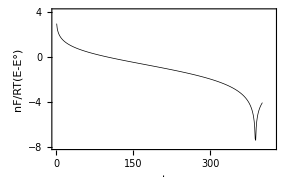

```mathematica
plot1=ListPlot[potentials,optionD,PlotRange->{{0,420},{-8,4}}]
```

Fig. Chapter.FigureCaption  Simulated constant current chronopotentiogram. Simulation parameters: D= 0.35, α=0.5, D=10^-5 cm^2 · s^-1, k_s=10^6 cm · s^-1, i=-0.9, n=400.

The ‘mess’ at the end of the plot is due to a problem that arises when the transition time is exceeded. Negative concentrations are predicted from eqn (Chapter.EquationNumbered) for t>τ. In fact eqn (Chapter.EquationNumbered) is applicable only for times less than or equal to the transition time. The way to get around this is simply to stop the simulation when the transition time is reached. This can be done by using NestWhileList instead of NestList. With this function the nesting continues only while a test returns true.

To use NestWhileList in the simulation a short test function needs to be written. We want the simulation to stop as soon as c_O_1^k, which is part ⟦1,1⟧ of the concentration list, is zero. NonNegative[#⟦1,1⟧]& becomes the test that is applied after each iteration.

```mathematica
conc=Table[{1.,0.},{m}];

c=NestWhileList[solveFor[#,𝔻,iDim]&,conc,NonNegative[#⟦1,1⟧]&,1,n,-1];
c=Rest[c];

eValues=Map[FindRoot[(i/ksDim)==#⟦2⟧*Exp[(1-α)*ℰ]-#⟦1⟧*Exp[-α*ℰ],{ℰ,5.}]&,c⟦All,1⟧];
potentials1=ℰ/.eValues;
```

The resulting plot is now nice and ‘clean.’

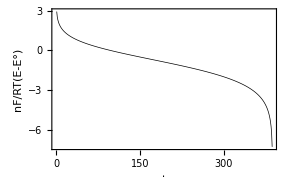

```mathematica
plot2=ListPlot[potentials1,optionD]
```

Fig. Chapter.FigureCaption  Simulated constant current chronopotentiogram. Simulation parameters: D= 0.35, α=0.5, D=10^-5 cm^2 · s^-1, k_s=10^6 cm^2 · s^-1, i=-0.9, n=400.

```mathematica
{Length[c],0.9*Sqrt[N[Length[c]/(n-1)]]}
```

{387,0.885254}

The transition time occurs after 387 of the 400 time increments therefore τ=387/400 and i τ^(1/2)=0.8853 (π^(1/2)/2=0.8862). We’ll save the data for the concentration profile at the transition time for use later in §Chapter.4.3.

```mathematica
Last[c]>>chrono.dat
```

### Chapter.Section.Subsection Current reversal experiment

To simulate a current reversal experiment a second test function is written. When the current is reversed we want the simulation to stop when c_R_1^k, which is part ⟦1,2⟧ of the concentration list, is zero. For a current reversal the simulation is simply continued after changing the sign on iDim.

```mathematica
iDim=-(2*i)/(√(𝔻*(n-1)));

c=NestWhileList[solveFor[#,𝔻,iDim]&,Last[c],NonNegative[#⟦1,2⟧]&,1,n,-1];
c=Rest[c];

eValues=Map[FindRoot[(i/ksDim)==#⟦2⟧*Exp[(1-α)*ℰ]-#⟦1⟧*Exp[-α*ℰ],{ℰ,5.}]&,c⟦All,1⟧];
potentials2=ℰ/.eValues;

(*join this data representing the reversal with the previous data set*)

potentials=Join[potentials1,potentials2];
```

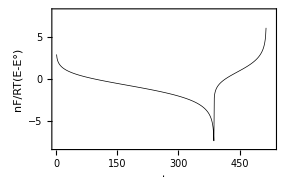

```mathematica
plot3=ListPlot[potentials,optionD,PlotRange-> {{0,530},{-8,8}}]
```

Fig. Chapter.FigureCaption  Simulated constant current chronopotentiogram. Simulation parameters: D= 0.35, α=0.5, D=10^-5 cm^2 · s^-1, k_s=10^6 cm · s^-1, i=-0.9, n=400.

The first transition time occurs after 387 time increments. The simulation finishes after the second transition time is reached. This occurs after another 129 time increments in agreement with eqn (Chapter.EquationNumbered).

```mathematica
{Length[potentials2],387/3}
```

{128,129}

### Chapter.Section.Subsection Two component system

For a two component system we have four concentrations to track therefore a list of elements with four parts { O_1, R_1, O_2, R_2} for every distance increment is required. We already have a list of concentrations for { O_1, R_1} at the first transition time. We can add the values of { O_2, R_2}, i.e. {1, 0}, to this list and use it as input for this simulation.

```mathematica
conc=<<chrono.dat;
```

```mathematica
(*convert {Subscript[O, 1],Subscript[R, 1]}to {Subscript[O, 1],Subscript[R, 1], Subscript[O, 2],Subscript[R, 2]}*)
conc=Map[{#⟦1⟧,#⟦2⟧,1.,0.}&,conc];
conc=conc/.{conc⟦1,1⟧-> 0.,conc⟦1,2⟧-> 1.};
```

An additional function is needed to stop the iteration when the surface concentration of O_2, the third element of the concentration list, is zero.

NonNegative[#⟦1,3⟧]&

Using the three point approximation for the fluxes we have

(3 c_(O_(1,1))^k-4 c_(O_(1,2))^k+c_(O_(1,3))^k)+(3 c_(O_(2,1))^k-4 c_(O_(2,2))^k+c_(O_(2,3))^k)=(2i)/(D(n-1))^(1/2)

where c_(O_(1,j))^k is the concentration of O_1 at the jth space increment and kth time increment. The concentrations c_(O_(1,2))^k, c_(O_(1,3))^k, c_(O_(2,2))^k, c_(O_(2,3))^k are known and at time t > τ_1 c_(O_(1,1))^k=0 therefore the surface concentration of O_2 at k, c_(O_(2,1))^k, is

c_(O_(2,1))^k=(2i)/(3(D(n-1))^(1/2))+4/3 c_(O_(1,2))^k-1/3 c_(O_(1,3))^k+4/3 c_(O_(2,2))^k-1/3 c_(O_(2,3))^k

Likewise the concentrations c_(R_(1,2))^k, c_(R_(1,3))^k, c_(R_(2,2))^k, c_(R_(2,3))^k are known and at time t > τ_1 c_(R_(1,1))^k=1 therefore the surface concentration of R_2 at k, c_(R_(2,1))^k, is

c_(R_(2,1))^k=-(2i)/(3(D(n-1))^(1/2))-1+4/3 c_(R_(1,2))^k-1/3 c_(R_(1,3))^k+4/3 c_(R_(2,2))^k-1/3 c_(R_(2,3))^k

The function to solve the concentrations for τ_1< t<τ_2 is slightly different to the one in the previous section due to these differing boundary calculations.

```mathematica
ClearAll[solveForSecond];

solveForSecond[list_List,α_,iDim_]:=Module[{tmp},

tmp=ListCorrelate[{{α},{(1.-2*α)},{α}},list];

(* add boundary values *)
Partition[Flatten[{0.,1.,(iDim+4*tmp⟦1,1⟧-tmp⟦2,1⟧+4*tmp⟦1,3⟧-tmp⟦2,3⟧)/3,(-iDim-3.+4*tmp⟦1,2⟧-tmp⟦2,2⟧+4*tmp⟦1,4⟧-tmp⟦2,4⟧)/3,tmp,1.,0.,1.,0.}],4]
];
```

solveForSecond is applied to the concentration list by NestWhileList. The maximum number of iterations is extended to 4n to allow time for the second transition time to be reached.

```mathematica
iDim=(2*i)/(√(𝔻*(n-1)));(*return it to its original value*)
c1=NestWhileList[solveForSecond[#,𝔻,iDim]&,conc,NonNegative[#⟦1,3⟧]&,1,4*n,-1];
c1=Rest[c1];
```

Finally the potential at each time increment is calculated. For simplicity it was assumed that dimensionless formal potential for the couple O_1/R_1 was zero for the calculation of the dimensionless potentials in §Chapter.4.1. The dimensionless formal potential of the second couple O_2/R_2 is sufficiently removed from that of the O_1/R_1 couple that the transition time for the first reaction is reached before the second reaction commences. To correct the dimensionless potentials calculated from τ_1< t< τ_2 the difference in the dimensionless formal potentials of the O_1/R_1 and O_2/R_2 redox couples is subtracted. In the example below it was assumed that the dimensionless formal potential of the second couple was -15 units.

```mathematica
eValues=Map[FindRoot[(i/ksDim)==#⟦4⟧*Exp[(1-α)*(ℰ+15)]-#⟦3⟧*Exp[-α*(ℰ+15)],{ℰ,5.}]&,c1⟦All,1⟧];
potentials3=ℰ/.eValues;
```

A simulated chronopotentiogram is shown below. The second transition time, 1162 increments, is almost three times that of the first transition time, 387 increments. The ratio of τ_2/τ_1=3 could be obtained by increasing the value of n.

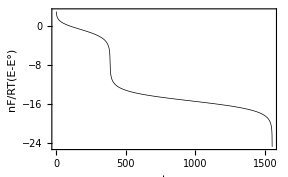

```mathematica
plot4=ListPlot[Join[potentials1,potentials3],optionE]
```

Fig. Chapter.FigureCaption  Constant current chronopotentiometry of a two component system. Simulation parameters: D= 0.35, α = 0.5, D = 10^-5 cm^2 · s^-1, k_s=10^6 cm · s^-1, i=-0.9, n=400.

## Chapter.Section Summary

This chapter has shown that chronopotentiometric methods can be simulated in an analogous manner to the voltammetric methods described in earlier chapters. The main difference in the chronopotentiometric simulations is the need to use FindRoot to numerically determine the potential at a given time increment.

## Further Reading

Britz, D. (1988). Digital Simulation in Electrochemistry, Springer-Verlag, Berlin.
Davis, D. G. (1966). Applications of Chronopotentiometry to Problems in Analytical Chemistry. In Electroanalytical Chemistry, Vol. 1. (ed. A. J. Bard), pp. 157-196, Marcel Dekker, New York.
Jain, R. K., Gaur, H. C., and Welch, B. J. (1977). Journal of Electroanalytical Chemistry, 79, 211-36.
Paunovic, M. (1967). Journal of Electroanalytical Chemistry, 14, 447-74.